## Cosmological Perturbation Theory Package

First, load the package

```mathematica
<<COSPER
```

Get::noopen: Cannot open "COSPER".

$Failed

Brief on-line help is available for all functions:

```mathematica
?IMetric
```

IMetric[g], with g an n.n-matrix (two lower indices),
  returns the inverse metric (two upper indices).

```mathematica
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

## Basic

### Background

First define the coordinate n-vector:

```mathematica
x={t,x1,x2,x3};
```

and then specify the metric as a square n×n matrix:

```mathematica
(met={{-a[t]*a[t],0,0,0},{0,a[t]*a[t],0,0},{0,0,a[t]*a[t],0},{0,0,0,a[t]*a[t]}})//MatrixForm;
```

"IMetric" is the only 1-argument function:

```mathematica
IMetric[met]//MatrixForm;
```

```mathematica
IMetric[met];
```

All other "functions" take two arguments, the metric matrix and then the coordinate vector:

```mathematica
Christoffel[met,x];
```

```mathematica
Riemann[met,x];
```

```mathematica
Ricci[met,x];
```

```mathematica
SCurvature[met,x]
```

(6 a''[t])/a[t]^3

```mathematica
FullSimplify[SCurvature[met,x]];
```

```mathematica
EinsteinTensor[met,x];
```

```mathematica
SqRicci[met,x];
```

```mathematica
SqRiemann[met,x];
```

```mathematica
(EMTensor={{-ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}})//MatrixForm;
```

Friedmann Equation

```mathematica
FriedmannClassic=EinsteinTensor[met,x][[1]][[1]]==κ^2 EMTensor[[1]][[1]];
```

## ΛCDM Model

Hubble function

```mathematica
HL[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=HCurrent √(Omegam0 a^-3+Omegar0 a^-4+OmegaL);
HL1[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=D[HL[a,HCurrent,Omegam0,Omegar0,OmegaL],a];
iHL[a_]:= H0  √(Ωm0 a^-1+ Ωx0 a^2)
```

```mathematica
HL[a,H0,Ωm0,Ωr0,Ωx0]
HL[a_]=HL[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a_]=HL1[a,H0,Ωm0,Ωr0,Ωx0]
HM[a_]=HL[a,H0,Ωm0,0,Ωx0]
HM1[a_]=HL1[a,H0,Ωm0,0,Ωx0]
HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]
```

H0 √(Ωm0/a^3+Ωr0/a^4+Ωx0)

H0 √(Ωm0/a^3+Ωr0/a^4+Ωx0)

(H0 (-(3 Ωm0)/a^4-(4 Ωr0)/a^5))/(2 √(Ωm0/a^3+Ωr0/a^4+Ωx0))

(H0 (-(3 Ωm0)/a^4-(4 Ωr0)/a^5))/(2 √(Ωm0/a^3+Ωr0/a^4+Ωx0))

H0 √(Ωm0/a^3+Ωx0)

-(3 H0 Ωm0)/(2 a^4 √(Ωm0/a^3+Ωx0))

(H0 (-3000000000000 Ωm0-4000000000000000 Ωr0))/(2 √(1000000000 Ωm0+1000000000000 Ωr0+Ωx0))

## f(R) Gravity

f(R) signature

```mathematica
Clear[R]
RR[a_,HCurrent_,Constant_,Omegam0_,Omegar0_,mass_]=3 HCurrent^2/c^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant mass^2/c^2
D[3 HCurrent^2/lightspeed^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant mass^2/lightspeed^2,a];
RR1[a_,HCurrent_,Omegam0_,Omegar0_,mass_]=(3 HCurrent^2 (-(3 Omegam0)/a^4-(4 Omegar0)/a^5))/c^2//Simplify
```

(2 Constant mass^2)/c^2+(3 HCurrent^2 (Omegam0/a^3+Omegar0/a^4))/c^2

-(3 HCurrent^2 (3 a Omegam0+4 Omegar0))/(a^5 c^2)

n is kinda special. Give the value of it first. Because when doing derivative

```mathematica
(*
Clear[f,fR]
(*fComp[Constant1_,Constant2_,mass_]=ffComp[4,Constant1,Constant2,mass]/.{R->R[a]};*)
f[Constant1_,Constant2_,mass_]=
fR[Constant1_,Constant2_,mass_]=ffR[1,Constant1,Constant2,mass]/.{R->R[a]}
fRR[Constant1_,Constant2_,mass_]=ffRR
*)
```

```mathematica
(*
Clear[f1,fR1,fR2]
f1[Constant1_,Constant2_,mass_]=Simplify[D[f[Constant1,Constant2,mass],a]]
fR1[Constant1_,Constant2_,mass_]=D[fR[Constant1,Constant2,mass],a]//Simplify
fR2[Constant1_,Constant2_,mass_]=D[D[fR[Constant1,Constant2,mass],a],a]
*)
```

Constants and fundamental functions. Units should be determined first.

```mathematica
Clear[Const1,Const2]
c=3*10^5;
h=0.71;
H0=100 h;
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
fR0=0.02;
d1=6 Ωx0/Ωm0;
d2=-fR0 (12/Ωm0-9)^2
m=H0 √Ωm0;
lp=√(2.47*10^-25);
Const1[nn_]=-(36(Ωx0/Ωm0)^2)/(12/Ωm0-9)^(nn+1)nn/fR0;
Const2[nn_]=-(6 Ωx0/Ωm0)/(12/Ωm0-9)^(nn+1)nn/fR0;
Ω=Ωm0 a^-3+Ωr0 a^-4;
Ω[a_]=Ω
R=3 H0^2 Ωm0 a^-3+12 Ωx0/Ωm0 m^2;
R1=RR1[a,H0,Ωm0,Ωr0,m];
(*
ρcr= (3 H0^2)/κ^2;
ρm[a_]=ρcr Ωm0 a^-3;
ρr[a_]=ρcr Ωr0 a^-4;
ρ[a_]=ρm[a]+ρr[a];
pm[a_]=0;
pr[a_]=1/3 ρr[a];
p[a_]=pm[a]+pr[a];
*)
Hubb[a_]:=HubbleL[Ωr0,Ωm0,Ωx0,H0,a];
```

-25.1262

Set::write: Tag Plus in (0.0000809/a^4 + 0.27/a^3)[a_] is Protected.

0.0000809/a^4+0.27/a^3

First equation: (Omega is the parameter for fraction evolution, so use )

```mathematica
f=-d1 m^2/c^2+d2 m^2/c^2 m^2/R-d2^2/d1 m^2(m^2/R)^2+d2^3/d1^2 m^2(m^2/R)^3
fR=-d2 m^4 1/R^2+2 d2^2/d1 m^2 m^4/R^3
fRR=2d2 m^4 1/R^3 c^2
3 (1+fR)==1/2 (-f+(1-fR) R)+κ^2 (ρm[a]+ρr[a])-3 a fRR H[a]^2 R'[a]
```

-2.45329×10^-7-(2.06862×10^14)/((44159.2+4083.21/a^3)^3)-(9.81259×10^10)/((44159.2+4083.21/a^3)^2)-0.000517184/(44159.2+4083.21/a^3)

(1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)

-(8.37837×10^18)/((44159.2+4083.21/a^3)^3)

3 (1+(1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2))==1/2 (2.45329×10^-7+(2.06862×10^14)/((44159.2+4083.21/a^3)^3)+(9.81259×10^10)/((44159.2+4083.21/a^3)^2)+0.000517184/(44159.2+4083.21/a^3)+(1-(1.96252×10^11)/((44159.2+4083.21/a^3)^3)-(4.65465×10^7)/((44159.2+4083.21/a^3)^2)) (44159.2+4083.21/a^3))+κ^2 (ρm[a]+ρr[a])+(2.51351×10^19 a H[a]^2 (44159.2+4083.21/a^3)'[a])/((44159.2+4083.21/a^3)^3)

## Background Comparison with LCDM model.

```mathematica
D[Ω,a]
```

-0.0003236/a^5-0.81/a^4

```mathematica
Hb[a_]=√((6 H0^2 Ω+(fR)(3 H0^2 Ω-2f)-f)/(6(1+fR+a fRR(3 H0^2 D[Ω,a])/(1+2fR))))
Hb2[a_]=(√(-f/6+1/6 fR R+H0^2 Ωm0 a^-3+H0^2 Ωr0 a^-4))/(√(1+fR+a fRR R1))
H[a_]=H0√((27 (Ωm0 a^-3)^4+(27*13 Ωx0-3d2)(Ωm0 a^-3)^3+(9*12*15 Ωx0^2-24d2 Ωx0)(Ωm0 a^-3)^2+(21*12^2 Ωx0^3-12*4d2 Ωx0^2)(Ωm0 a^-3)+Ωx0 (12Ωx0)^3+Ωr0 a^-4(27 (Ωm0 a^-3)^3+(12Ωx0)^3+3(3 Ωm0 a^-3)^2 12Ωx0+3(12Ωx0)^2 3Ωm0 a^-3))/(27 (Ωm0 a^-3)^3+27*12 Ωx0 (Ωm0 a^-3)^2+(9*12^2 Ωx0^2-3d2 Ωm0^2-54 d2 Ωm0^2)Ωm0 a^-3+(12 Ωx0)^3-12d2 Ωm0^2 Ωx0))
```

1/(√6)(√((2.45329×10^-7+(-2 (-2.45329×10^-7-(2.06862×10^14)/((44159.2+4083.21/a^3)^3)-(9.81259×10^10)/((44159.2+4083.21/a^3)^2)-0.000517184/(44159.2+4083.21/a^3))+15123. (0.0000809/a^4+0.27/a^3)) ((1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2))+30246. (0.0000809/a^4+0.27/a^3)+(2.06862×10^14)/((44159.2+4083.21/a^3)^3)+(9.81259×10^10)/((44159.2+4083.21/a^3)^2)+0.000517184/(44159.2+4083.21/a^3))/(1+(1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)-(1.26706×10^23 (-0.0003236/a^5-0.81/a^4) a)/((1+2 ((1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2))) (44159.2+4083.21/a^3)^3))))

(√(1/6 (2.45329×10^-7+(2.06862×10^14)/((44159.2+4083.21/a^3)^3)+(9.81259×10^10)/((44159.2+4083.21/a^3)^2)+0.000517184/(44159.2+4083.21/a^3))+1/6 ((1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)) (44159.2+4083.21/a^3)+0.407817/a^4+1361.07/a^3))/(√(1+(1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)+(1.40785×10^12 (0.0003236+0.81 a))/((44159.2+4083.21/a^3)^3 a^4)))

71. √((490.722+0.143489/a^12+6.52705/a^9+95.0258/a^6+(0.0000809 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^4+491.156/a^3)/(688.267+0.531441/a^9+17.2423/a^6+214.662/a^3))

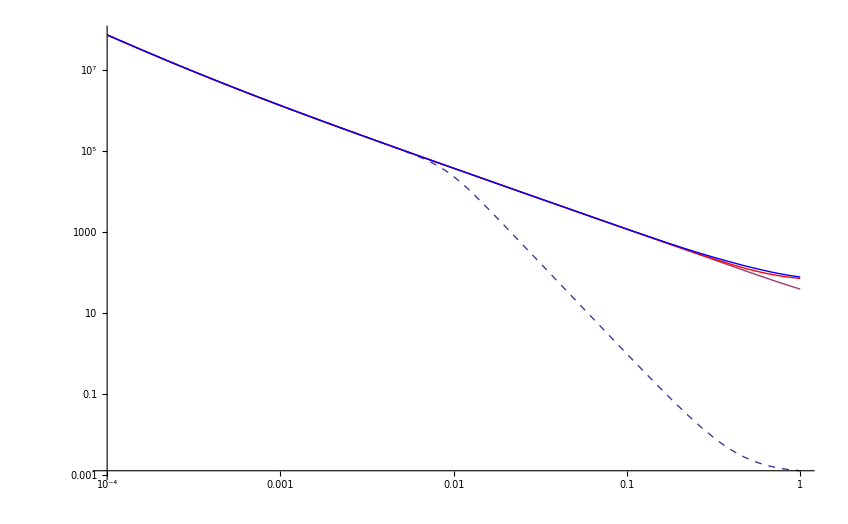

```mathematica
LogLogPlot[{Hb[a],Hb2[a],HL[a,H0,Ωm0,Ωr0,Ωx0],H[a]},{a,10^-4,1},PlotStyle->{Dashed,Thick,Red,Blue}]
```

```mathematica
H1[aa]/H[aa]//Simplify
```

(0.0140845 H1[aa])/(√((0.0000429936+0.143489 aa+0.0013949 aa^3+6.52705 aa^4+0.0150856 aa^6+95.0258 aa^7+0.0543827 aa^9+491.156 aa^10+490.722 aa^13)/(aa^4 (0.531441+17.2423 aa^3+214.662 aa^6+688.267 aa^9))))

H1[a] is the first derivative of H[a]

```mathematica
H1[a_]=D[H[a],a];
wleff[a_]=-1-2/3 a HL1[a]/HL[a]
wmeff[a_]=-1-2/3 a HM1[a]/HM[a]
weff[a_]=-1-2/3 a H1[a]/H[a]
```

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

-1+0.27/((0.73+0.27/a^3) a^3)

-1-(0.333333 ((-1.72187/a^13-58.7435/a^10-570.155/a^7-(0.0003236 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^5-1473.47/a^4+(0.0000809 (-4.78297/a^10-103.454/a^7-559.417/a^4))/a^4)/(688.267+0.531441/a^9+17.2423/a^6+214.662/a^3)-((-4.78297/a^10-103.454/a^7-643.987/a^4) (490.722+0.143489/a^12+6.52705/a^9+95.0258/a^6+(0.0000809 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^4+491.156/a^3))/((688.267+0.531441/a^9+17.2423/a^6+214.662/a^3)^2)) (688.267+0.531441/a^9+17.2423/a^6+214.662/a^3) a)/(490.722+0.143489/a^12+6.52705/a^9+95.0258/a^6+(0.0000809 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^4+491.156/a^3)

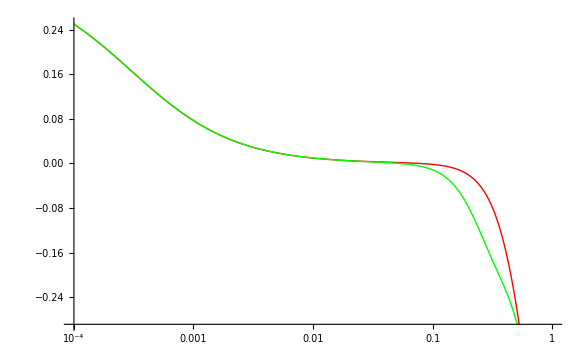

```mathematica
LogLinearPlot[{wleff[a],weff[a]},{a,0.0001,1},PlotStyle->{Red,Green,Blue}]
```

```mathematica
weff[0.3]
H1[0.1]
HL1[0.3]
HL[0.3]
H[0.3]
```

-0.162061

-17434.6

-1084.69

232.681

252.726

```mathematica
fRplot[a_]=fR
```

(1.96252×10^11)/((44159.2+4083.21/a^3)^3)+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)

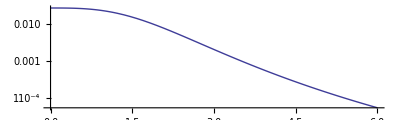

```mathematica
LogPlot[fRplot[1/mn],{mn,10^-4,6},AspectRatio-> 0.3]
```

## f(R) Gravity Perturbation

LCDM Model data

138

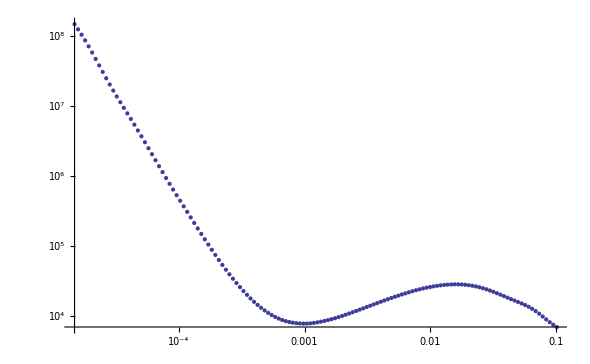

NIntegrate::nlim: temp = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

```mathematica
Clear[GrowthL]
PowerL=Import["cdm_invariant_cut.dat"];
lent=Length[PowerL]
ListLogLogPlot[PowerL]
GrowthL[a_]:= 5/2 Ωm0  HL[a,H0,Ωm0,Ωr0,Ωx0]/H0 NIntegrate[1/(iHL[temp]/H0)^3,{temp,0,a}];
GrowthL1[a_]=D[GrowthL[a],a];
```

Check the divation from LCDM : M

((4083.21+44159.2 a^3)^3 (6.80777×10^10+2.20874×10^12 a^3+3.42107×10^22 a^6+3.69982×10^23 a^9-3.35135×10^19 a^7 kk^2))/((6.80777×10^10+2.20874×10^12 a^3+2.40772×10^13 a^6+8.83635×10^13 a^9) (6.80777×10^10+2.20874×10^12 a^3+3.42107×10^22 a^6+3.69982×10^23 a^9-2.51351×10^19 a^7 kk^2))

0.978715

0.978715

0.97871

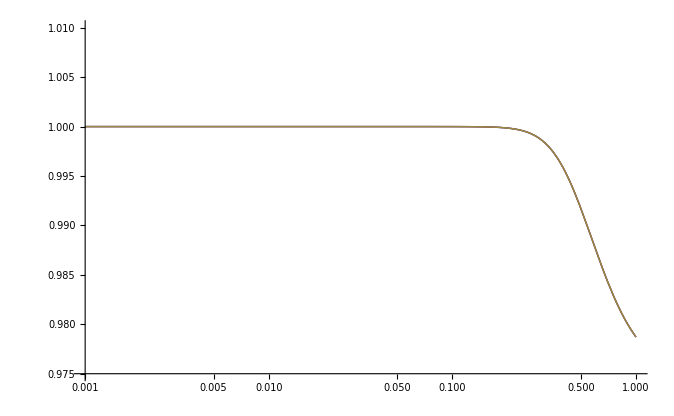

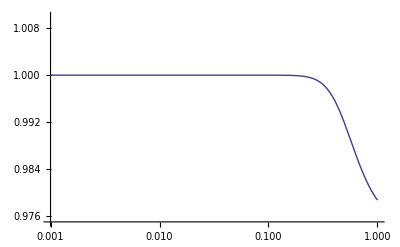
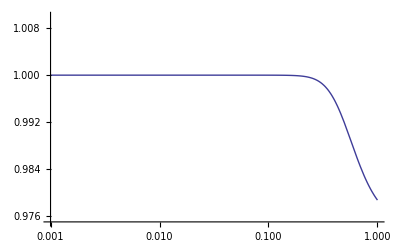
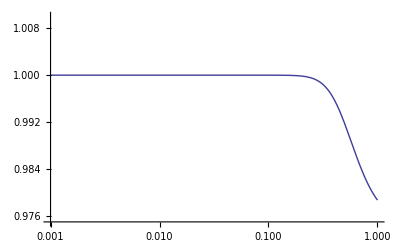

```mathematica
Clear[k,a,dH,dHL,temp,chih2]
dH[a_?NumberQ]:= c a NIntegrate[1/(temp^2 H[temp]),{temp,0,a}]
dHL[a_?NumberQ]:=c a NIntegrate[1/(temp^2 HL[temp]),{temp,0,a}]
k[a_]:=1/dH[a]
kL[a_]:=1/dHL[a]
chih2[a_,kk_]=1/(fR+1)(4fRR+(fR+1-R fRR)a^2/kk^2)/(3fRR+(fR+1-R fRR)a^2/kk^2)//Simplify
chih2[1,0.01]
chih2[1,0.1]
chih2[1,0.5]
LogLinearPlot[{chih2[a,0.001],chih2[a,0.01],chih2[a,0.1]},{a,0.001,1},PlotRange->{0.975,1.01}]
Table[{LogLinearPlot[chih2[a,0.001],{a,0.001,1},PlotRange->{0.975,1.01}],LogLinearPlot[chih2[a,0.01],{a,0.001,1},PlotRange->{0.975,1.01}],LogLinearPlot[chih2[a,0.1],{a,0.001,1},PlotRange->{0.975,1.01}]}]
```

```mathematica
(*
xx[a_]=Block[{kk,gg},kk=h PowerL[[100,1]];NDSolve[{a^2*gg''[a]+a^2*(H1[a]/H[a]+3/a)gg'[a]-3/2 chih2[a,kk] H0^2 Ωm0 a^-3/H[a]^2 gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-3]==GrowthL'[10^-3]},gg[a],{a,0.001,10}][[1]][[1]]]
xx[10]
xxx[a_]=Block[{kk=h PowerL[[nn,1]]},NDSolve[{a^2×∂_(a,a) DgL[a]+3/2×a×(1+H[a]^-2×H0^2×Ωx0)×∂_a DgL[a]-3/2×chih2[a,kk]*H[a]^-2×H0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL[a],{a,0.001,1}][[1]][[1]]];
xxxx[a_]=Block[{kk=h PowerL[[1,1]]},NDSolve[{∂_(a,a) DgL[a]+(3/a+HL1[a]/HL[a])×∂_a DgL[a]-3/2 1/(a^2 HL[a]^2)H0^2×(Ωm0 a^-3+Ωx0)×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL[a],{a,0.001,1}][[1]][[1]]];
*)
```

```mathematica
xx[0.1]
GrowthL[0.01]
```

xx[0.1]

0.0101487

```mathematica
PowerL[[nn,1]]==k[an];
```

Part::pspec: Part specification nn is neither an integer nor a list of integers.

```mathematica
solgf=NDSolve[{a^2*gg''[a]+a^2*(H1[a]/H[a]+3/a-Ωx0/H[a]^2)gg'[a]-3/2 H0^2 Ωm0 a^-3/H[a]^2 gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-4]==GrowthL'[10^-4]},gg[a],{a,0.001,1}][[1]]
Growth[a_]=gg[a]/.solgf[[1]]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{gg[a]→InterpolatingFunction[{{0.001,1.}},<>][a]}

InterpolatingFunction[{{0.001,1.}},<>][a]

```mathematica
solgft=NDSolve[{a^2*ggt''[a]+a^2*(H1[a]/H[a]+3/a)ggt'[a]-3/2 H0^2 Ωm0 a^-3/H[a]^2 ggt[a]==0,ggt[10^-3]==GrowthL[10^-3],ggt'[10^-3]==GrowthL'[10^-3]},ggt[a],{a,0.001,1}][[1]]
Growtht[a_]=ggt[a]/.solgft[[1]]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{ggt[a]→InterpolatingFunction[{{0.001,1.}},<>][a]}

InterpolatingFunction[{{0.001,1.}},<>][a]

```mathematica
solgfl=NDSolve[{a^2*ggl''[a]+a^2*(HL1[a]/HL[a]+3/a)ggl'[a]-3/2 H0^2 Ωm0 a^-3/HL[a]^2 ggl[a]==0,ggl[10^-3]==GrowthL[10^-3],ggl'[10^-3]==GrowthL'[10^-3]},ggl[a],{a,0.001,1}][[1]]
Growthl[a_]=ggl[a]/.solgfl[[1]]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{ggl[a]→InterpolatingFunction[{{0.001,1.}},<>][a]}

InterpolatingFunction[{{0.001,1.}},<>][a]

NIntegrate::nlim: temp = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.217158} lies outside the range of data in the interpolating function. Extrapolation will be used.

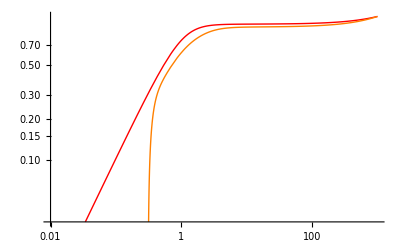

InterpolatingFunction::dmval: Input value {-0.217158} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

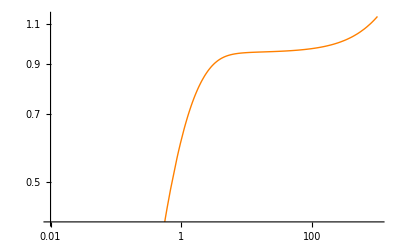
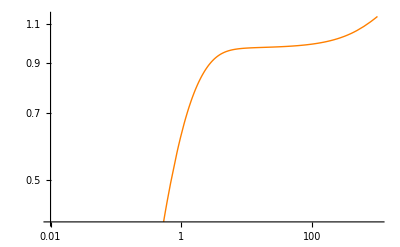
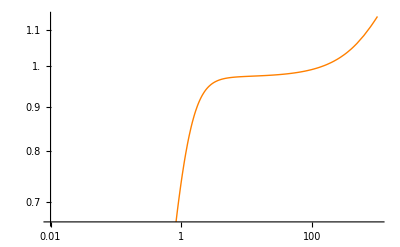

```mathematica
LogLogPlot[{mn GrowthL[1/mn],mn Growth[1/mn]},{mn,0.01,1000},PlotStyle->{Red,Orange},PlotLegend->{"LCDM_L", "f(R)"},LegendPosition->{1.1,-0.4}]
Table[{LogLogPlot[mn Growth[1/mn],{mn,0.01,1000},PlotStyle->Orange,PlotLegend->"f(R)",LegendPosition->{1.1,-0.4}],LogLogPlot[mn Growtht[1/mn],{mn,0.01,1000},PlotStyle->Orange,PlotLegend->"f(R)",LegendPosition->{1.1,-0.4}],LogLogPlot[mn Growthl[1/mn],{mn,0.01,1000},PlotStyle->Orange,PlotLegend->"LCDM Test",LegendPosition->{1.1,-0.4}]}]
```

```mathematica
ain=Table[ai/.FindRoot[PowerL[[i,1]]h==k[ai],{ai,0.0001}],{i,1,lent}]
aL=Table[aL/.FindRoot[PowerL[[i,1]]h==kL[aL],{aL,0.0001}],{i,1,lent}]
```

{5.5385,5.20935,4.90078,4.6115,4.34029,4.08603,3.84765,3.62416,3.41462,3.21816,3.03396,2.86124,2.69929,2.54741,2.40498,2.2714,2.14609,2.02855,1.91826,1.81476,1.71762,1.62641,1.54077,1.46031,1.3847,1.31361,1.24676,1.18384,1.1246,1.0688,1.0162,0.966585,0.919759,0.875534,0.83374,0.794218,0.75682,0.721409,0.687861,0.656059,0.625896,0.597272,0.570095,0.54428,0.519748,0.496425,0.474243,0.453139,0.433054,0.413932,0.395722,0.378375,0.361846,0.346092,0.331073,0.316751,0.30309,0.290056,0.277618,0.265745,0.254408,0.243581,0.233238,0.223355,0.21391,0.20488,0.196247,0.187991,0.180093,0.172538,0.165309,0.158391,0.15177,0.145432,0.139364,0.133555,0.127993,0.122666,0.117565,0.112679,0.108,0.103518,0.0992241,0.095111,0.0911707,0.0873958,0.0837791,0.080314,0.0769939,0.0738128,0.0707647,0.0678439,0.0650452,0.0623633,0.0597933,0.0573305,0.0549704,0.0527087,0.0505411,0.0484639,0.046473,0.0445651,0.0427365,0.0409839,0.0393041,0.0376942,0.0361511,0.0346721,0.0332544,0.0318956,0.0305931,0.0293447,0.028148,0.0270008,0.0259011,0.024847,0.0238365,0.0228678,0.0219391,0.0210488,0.0201953,0.0193771,0.0185926,0.0178405,0.0171194,0.016428,0.0157651,0.0151295,0.01452,0.0139357,0.0133753,0.012838,0.0123228,0.0118287,0.0113548,0.0109005,0.0104647,0.0100468}

{5.28897,4.97449,4.67966,4.40327,4.14415,3.90122,3.67348,3.45997,3.25979,3.07212,2.89616,2.73119,2.57651,2.43147,2.29547,2.16794,2.04834,1.93617,1.83096,1.73226,1.63966,1.55276,1.4712,1.39463,1.32273,1.25519,1.19172,1.13206,1.07594,1.02313,0.973413,0.926571,0.88241,0.840749,0.801416,0.764254,0.729113,0.695859,0.664364,0.634511,0.606192,0.579308,0.553767,0.529484,0.506383,0.484391,0.463442,0.443476,0.424438,0.406274,0.388937,0.372384,0.356573,0.341465,0.327025,0.31322,0.300019,0.287392,0.275313,0.263754,0.252693,0.242107,0.231973,0.222271,0.212983,0.204088,0.195571,0.187415,0.179603,0.172121,0.164955,0.15809,0.151514,0.145215,0.139181,0.133399,0.127861,0.122554,0.11747,0.112599,0.107932,0.10346,0.0991755,0.0950699,0.091136,0.0873664,0.0837542,0.0802929,0.0769761,0.0737977,0.0707519,0.0678332,0.0650361,0.0623556,0.0597868,0.057325,0.0549658,0.0527047,0.0505378,0.048461,0.0464707,0.044563,0.0427347,0.0409824,0.0393029,0.0376931,0.0361502,0.0346713,0.0332538,0.0318951,0.0305927,0.0293443,0.0281476,0.0270005,0.0259009,0.0248468,0.0238363,0.0228677,0.021939,0.0210487,0.0201953,0.019377,0.0185925,0.0178404,0.0171193,0.0164279,0.015765,0.0151294,0.01452,0.0139356,0.0133753,0.012838,0.0123227,0.0118287,0.0113548,0.0109004,0.0104647,0.0100468}

```mathematica
Export["ModifiedGravity\\fRGravity\\Data\\ain.xls",ain,"XLS"]
Export["ModifiedGravity\\fRGravity\\Data\\aL.xls",aL,"XLS"]
```

ModifiedGravity\fRGravity\Data\ain.xls

ModifiedGravity\fRGravity\Data\aL.xls

Find the transition points & fractions

```mathematica
trans=29;transL=28;
frac:=1/((Growth[1]/Growth[ain[[lent]]])/(GrowthL[1]/GrowthL[aL[[lent]]]));
```

Q factors

```mathematica
qFactor=Table[{PowerL[[i+trans,1]],frac(Growth[1]/Growth[ain[[i+trans]]])/(GrowthL[1]/GrowthL[aL[[i+trans]]])},{i,1,lent-trans}];
qFactorEx=Table[{PowerL[[i,1]],frac(Growth[1]/Growth[ain[[trans]]])/(GrowthL[1]/GrowthL[aL[[trans]]])},{i,1,trans}];
```

InterpolatingFunction::dmval: Input value {1.0688} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.0162} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.1246} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
qFactor;
```

```mathematica
qFactorEx;
```

```mathematica
qFac=Join[qFactorEx,qFactor];
```

```mathematica
power=Table[{PowerL[[i,1]],(qFac[[i]][[2]])^2 PowerL[[i,2]]},{i,1,lent}];
Export["ModifiedGravity\\fRGravity\\Data\\Power.xls",power,"XLS"]
```

ModifiedGravity\fRGravity\Data\Power.xls

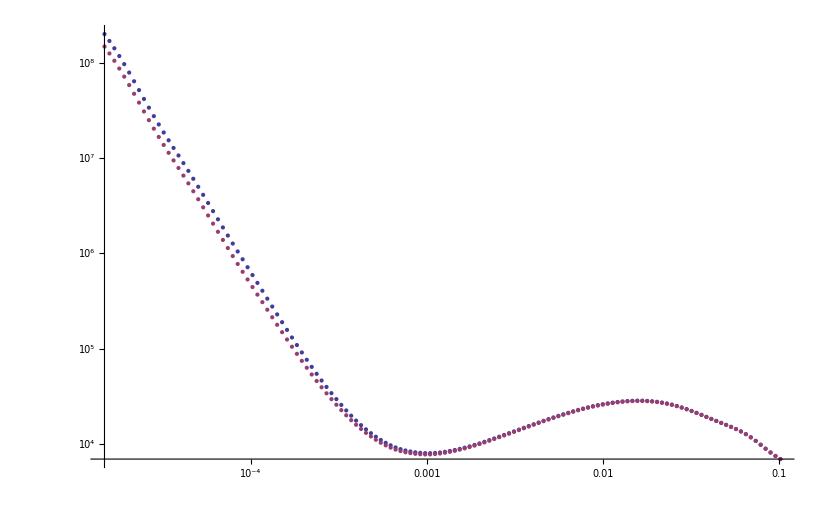

```mathematica
ListLogLogPlot[{power,PowerL}]
```

{{0.0000147064,0.162768},{0.0000156873,0.162768},{0.0000167336,0.162768},{0.0000178496,0.162768},{0.0000190402,0.162768},{0.0000203101,0.162768},{0.0000216647,0.162768},{0.0000231097,0.162768},{0.000024651,0.162768},{0.0000262952,0.162768},{0.000028049,0.162768},{0.0000299197,0.162768},{0.0000319153,0.162768},{0.0000340439,0.162768},{0.0000363146,0.162768},{0.0000387366,0.162768},{0.0000413202,0.162768},{0.0000440762,0.162768},{0.0000470159,0.162768},{0.0000501517,0.162768},{0.0000534967,0.162768},{0.0000570647,0.162768},{0.0000608708,0.162768},{0.0000649306,0.162768},{0.0000692613,0.162768},{0.0000738808,0.162768},{0.0000788084,0.162768},{0.0000840647,0.162768},{0.0000896716,0.162768},{0.0000956524,0.159309},{0.000102032,0.155591},{0.000108837,0.151619},{0.000116096,0.147397},{0.00012384,0.142938},{0.000132099,0.138257},{0.00014091,0.133375},{0.000150308,0.128315},{0.000160333,0.123105},{0.000171027,0.117775},{0.000182434,0.112357},{0.000194602,0.106884},{0.000207581,0.101389},{0.000221426,0.0959032},{0.000236194,0.0904594},{0.000251948,0.0850869},{0.000268752,0.0798136},{0.000286677,0.0746649},{0.000305797,0.069664},{0.000326193,0.0648314},{0.000347949,0.0601851},{0.000371156,0.0557403},{0.000395911,0.0515095},{0.000422317,0.0475022},{0.000450484,0.0437251},{0.00048053,0.0401822},{0.00051258,0.0368745},{0.000546768,0.0338006},{0.000583235,0.0309565},{0.000622135,0.028336},{0.00066363,0.0259314},{0.000707892,0.0237329},{0.000755106,0.0217301},{0.000805469,0.0199114},{0.000859191,0.0182647},{0.000916496,0.0167779},{0.000977624,0.0154387},{0.00104283,0.014235},{0.00111238,0.0131553},{0.00118657,0.0121883},{0.00126571,0.0113236},{0.00135013,0.0105513},{0.00144018,0.00986219},{0.00153624,0.00924773},{0.0016387,0.00870015},{0.001748,0.00821231},{0.00186458,0.00777773},{0.00198895,0.00739053},{0.0021216,0.00704539},{0.00226311,0.00673753},{0.00241405,0.00646266},{0.00257506,0.00621692},{0.00274681,0.00599688},{0.00293001,0.00579947},{0.00312543,0.00562192},{0.00333389,0.00546181},{0.00355625,0.00531695},{0.00379344,0.00518541},{0.00404645,0.00506547},{0.00431633,0.00495559},{0.00460422,0.00485442},{0.0049113,0.00476075},{0.00523887,0.00467349},{0.00558829,0.00459168},{0.00596101,0.00451448},{0.00635859,0.00444112},{0.00678269,0.00437091},{0.00723507,0.00430324},{0.00771763,0.00423757},{0.00823237,0.0041734},{0.00878144,0.00411028},{0.00936714,0.00404782},{0.0099919,0.00398564},{0.0106583,0.00392342},{0.0113692,0.00386083},{0.0121275,0.0037976},{0.0129364,0.00373346},{0.0137992,0.00366817},{0.0147195,0.0036015},{0.0157013,0.00353323},{0.0167485,0.00346315},{0.0178656,0.00339106},{0.0190571,0.00331677},{0.0203282,0.00324008},{0.021684,0.00316083},{0.0231303,0.00307883},{0.024673,0.0029939},{0.0263186,0.00290587},{0.028074,0.00281456},{0.0299464,0.00271978},{0.0319438,0.00262137},{0.0340743,0.00251914},{0.0363469,0.0024129},{0.0387712,0.00230248},{0.0413571,0.00218767},{0.0441155,0.00206828},{0.0470578,0.00194412},{0.0501964,0.00181497},{0.0535444,0.00168063},{0.0571156,0.00154087},{0.0609251,0.00139548},{0.0649886,0.00124422},{0.0693231,0.00108685},{0.0739467,0.000923124},{0.0788787,0.000752792},{0.0841397,0.000575589},{0.0897515,0.000391245},{0.0957377,0.000199479},{0.102123,-1.11022×10^-16}}

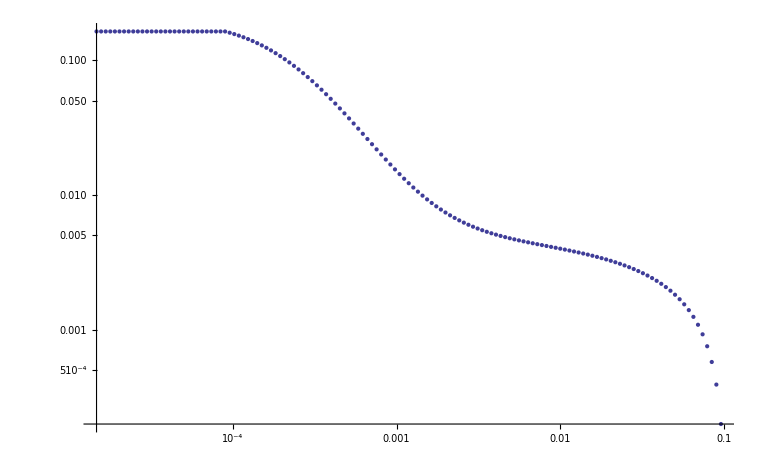

```mathematica
deltaqFac=Table[{qFac[[i,1]],qFac[[i,2]]-1},{i,1,lent}]
ListLogLogPlot[deltaqFac]
```

## Backup here

```mathematica
Clear[H]
fRFriedmann=3(1+fR)==3 H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3a H[a]^2 fRR R1//FullSimplify
```

1/(a (4083.21+44159.2 a^3))(-0.925442+a (-1.38988×10^14+a^2 (-30.0254+a (-6.01231×10^15+a^2 (-324.72-9.71417×10^16 a-1170.59 a^3-6.94559×10^17 a^4-1.8536×10^18 a^7))))+a^9 (1.36674×10^9+3.42107×10^12 a) H[a]^2)==0

```mathematica
Solve[ H[a]^2==(3 c^2)/(3a fRR R1) H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3(1+fR),H[a]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H[a]→-1.67634×10^-52 √(7.85609×10^107-(1.50539×10^119)/((44159.2+4083.21/a^3)^3)-(3.48314×10^115)/((44159.2+4083.21/a^3)^2)+(9.20216×10^99)/(44159.2+4083.21/a^3)+(8.87661×10^104)/(0.0003236+0.81 a)+(7.01762×10^101)/((0.0003236+0.81 a) a^9)+(2.3421×10^105)/((0.0003236+0.81 a) a^8)+(2.27683×10^103)/((0.0003236+0.81 a) a^6)+(7.59881×10^106)/((0.0003236+0.81 a) a^5)+(7.26518×10^106)/a^3-(1.42581×10^118)/((44159.2+4083.21/a^3)^3 a^3)-(3.38169×10^114)/((44159.2+4083.21/a^3)^2 a^3)+(2.46235×10^104)/((0.0003236+0.81 a) a^3)+(8.21797×10^107)/((0.0003236+0.81 a) a^2)+(2.96253×10^108 a)/(0.0003236+0.81 a))},{H[a]→1.67634×10^-52 √(7.85609×10^107-(1.50539×10^119)/((44159.2+4083.21/a^3)^3)-(3.48314×10^115)/((44159.2+4083.21/a^3)^2)+(9.20216×10^99)/(44159.2+4083.21/a^3)+(8.87661×10^104)/(0.0003236+0.81 a)+(7.01762×10^101)/((0.0003236+0.81 a) a^9)+(2.3421×10^105)/((0.0003236+0.81 a) a^8)+(2.27683×10^103)/((0.0003236+0.81 a) a^6)+(7.59881×10^106)/((0.0003236+0.81 a) a^5)+(7.26518×10^106)/a^3-(1.42581×10^118)/((44159.2+4083.21/a^3)^3 a^3)-(3.38169×10^114)/((44159.2+4083.21/a^3)^2 a^3)+(2.46235×10^104)/((0.0003236+0.81 a) a^3)+(8.21797×10^107)/((0.0003236+0.81 a) a^2)+(2.96253×10^108 a)/(0.0003236+0.81 a))}}

```mathematica
Clear[Sol]
Sol[a_]=NDSolve[{fRFriedmann,H[10^-3]==HL[10^-3,H0,Ωm0,Ωr0,Ωx0],H'[10^-3]==HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]},H[a],{a,10^-4,1}]
```

NDSolve::ivcon: The given initial conditions were not consistent with the differential-algebraic equations. NDSolve will attempt to correct the values.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

Testing Functions

```mathematica
t1=Table[i*10^-4,{i,1,10,0.1}];
t2=Table[i*10^-3,{i,1,10,0.1}];
t3=Table[i*10^-2,{i,1,10,0.1}];
t4=Table[i*10^-1,{i,1,10,0.1}];
t5=Table[i,{i,1,1,0.1}];
aTable=Join[t1,t2,t3,t4,t5];
Length[aTable]
ListPlot[aTable];
```

365

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

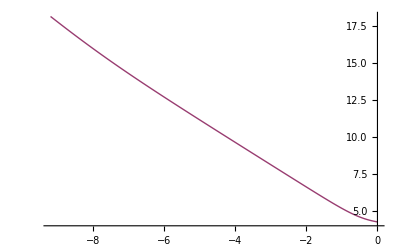

```mathematica
HubbleTable=Table[{Sol[aTable[[i]]][[1]][[1]],HL[aTable[[i]],H0,Ωm0,Ωr0,Ωx0],aTable[[i]]},{i,1,365}];
ListPlot[{Table[{Log[HubbleTable[[i]][[3]]],Log[H[HubbleTable[[i]][[3]]]/.HubbleTable[[i]][[1]]]},{i,1,365}],Table[{Log[HubbleTable[[i]][[3]]],Log[HubbleTable[[i]][[2]]]},{i,1,365}]},Joined->True]
```

ΛCDM as an example

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

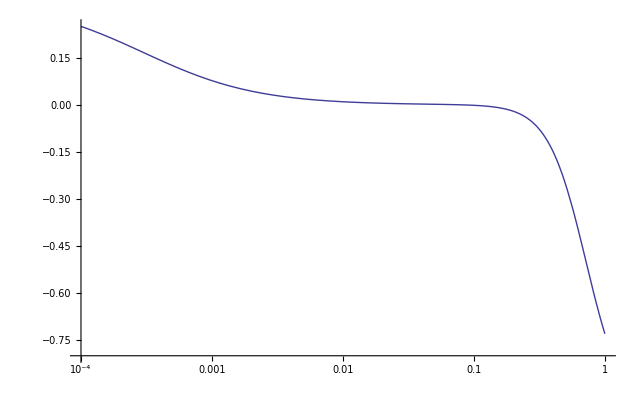

-194729.+3.56799×10^8 a^(1/9)-1.18914×10^9 a^(1/8)+1.55755×10^9 a^(1/7)-1.01651×10^9 a^(1/6)+3.45971×10^8 a^(1/5)-5.86945×10^7 a^(1/4)+4.31573×10^6 a^(1/3)-101465. √a+382.796 a

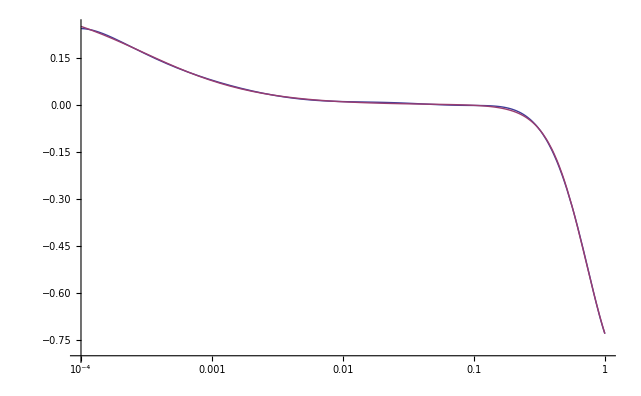

```mathematica
wleff[a_]=-1-2(a HL[a,H0,Ωm0,Ωr0,Ωx0] HL1[a,H0,Ωm0,Ωr0,Ωx0])/(3 HL[a,H0,Ωm0,Ωr0,Ωx0]^2)
LogLinearPlot[wleff[a],{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
wlefff=Table[{aTable[[i]],wleff[aTable[[i]]]},{i,1,365}];
wlefffit[a_]=Fit[wlefff,{1,a,a^(1/2),a^(1/3),a^(1/4),a^(1/5),a^(1/6),a^(1/7),a^(1/8),a^(1/9)},a]
LogLinearPlot[{wlefffit[a],wleff[a]},{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
```

```mathematica
H1[a_]=D[H[a]/.Sol[a][[1]][[1]],a];
H[a_]=H[a]/.Sol[a][[1]][[1]];
LogLogPlot[{H[a],Abs[H1[a]]},{a,10^-4,1}];
LogLogPlot[Abs[H1[a]],{a,10^-4,1}];
weff[xx_]=-1-2(H[1/xx] H1[1/xx])/(xx 3 H[1/xx]^2);
LogLinearPlot[weff[a],{a,10^-4,1}]
wefff=Table[{aTable[[i]],weff[aTable[[i]]]},{i,1,365}];
wefffit[xx_]=Fit[wefff,{1,xx,xx^2,xx^3,xx^4,xx^5},xx]
(*wefffit[a_]=Fit[wefff,{1,a^-1,a^(-1/2),a^(-1/3),a^(-1/4),a^(-1/5)},a]*)
LogLinearPlot[{wefffit[a],weff[a]},{a,10^-4,1}]
```

Part::partw: Part 1 of {} does not exist.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.21034 is not a valid variable.

General::ivar: -9.02955 is not a valid variable.

General::ivar: -8.83356 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: -9.21015 is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.02219 is not a valid variable.

General::ivar: -8.83422 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: 1/xx is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: 1/a is not a valid variable.

General::ivar: -0.108576 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

0.28152 xx^4 (9.71409 (-1-(6666.67 ∂_10000. Hold[H[1/0.0001]])/Hold[H[1/0.0001]])+9.70173 (-1-(6060.61 ∂_9090.91 Hold[H[1/0.00011]])/Hold[H[1/0.00011]])+9.68938 (-1-(«18»«1»«1»«1»)/Hold[«1»])+«498»)+0.215639 xx^2 («1»)+0.0523424 («1»)+«1»+0.307159 xx^5 («577»+«18» «1»)+0.251651 xx^3 («585»+140.096 (-1-(«19» ∂_(«1») «1»)/Hold[H[1/(«3»)]]))

General::ivar: 1/a is not a valid variable.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
TTT[a_]=(-d2 (1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^2))/(2d2 1/m^2 1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^3))-3 H0^2(Ωm0 a^-3+Ωr0 a^-4)-2d1 m^2)a^2
TTT[10^-3]
TTT[10^-2]
TTT[10^-1]
TTT[1]
```

(-44159.2-680.535 (32.4444+11.1111 (0.0000809/a^4+0.27/a^3))-15123. (0.0000809/a^4+0.27/a^3)) a^2

-7.95999×10^6

-630840.

-62094.1

-72365.4